```mathematica
SetDirectory[NotebookDirectory[]]
```

/Users/yinshi/Documents/work/post-doc-Humboldt/github/fluc_T/fluctuations_T/highorder_2p1/input_h/finitemub_v4/sigma_mass/Tc220alphap56

### Lattice

```mathematica
HotQCDp=Flatten[Import["../../../../../LQCDdata/hotPT4.dat"]];
HotQCDT=Flatten[Import["../../../../../LQCDdata/hotT.dat"]];
HotQCDperrdown=Flatten[Import["../../../../../LQCDdata/hotdpt4d.dat"]];
HotQCDperrup=Flatten[Import["../../../../../LQCDdata/hotdpt4u.dat"]];
Tcl=1;
Hotpdown=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrdown}];
Hotpup=Transpose[{HotQCDT/Tcl,HotQCDp+HotQCDperrup}];
WBp=Flatten[Import["../../../../../LQCDdata/wbpt4.dat"]];
WBdp=Flatten[Import["../../../../../LQCDdata/wbdpt4.dat"]];
WBT=Flatten[Import["../../../../../LQCDdata/wbT.dat"]];
WBdown=Transpose[{WBT/Tcl,WBp-WBdp}];
WBup=Transpose[{WBT/Tcl,WBp+WBdp}];
WBcs=Table[Import["../../../../../LQCDdata/WB-EoS.dat"][[i]][[-2]],{i,2,63}];
WBcserr=Table[Import["../../../../../LQCDdata/WB-EoS.dat"][[i]][[-1]],{i,2,63}];
WBcsup=Transpose[{WBT/Tcl,WBcs+WBcserr}];
WBcsdown=Transpose[{WBT/Tcl,WBcs-WBcserr}];
WBp2025=Flatten[Import["../../../../../LQCDdata/WB2025/PT4WB.dat"]];
WBdp2025=Flatten[Import["../../../../../LQCDdata/WB2025/PT4WB_erro.dat"]];
WBT2025=Flatten[Import["../../../../../LQCDdata/WB2025/TWB.dat"]];
WBdown2025=Transpose[{WBT2025/Tcl,WBp2025-WBdp2025}];
WBup2025=Transpose[{WBT2025/Tcl,WBp2025+WBdp2025}];
```

### Model

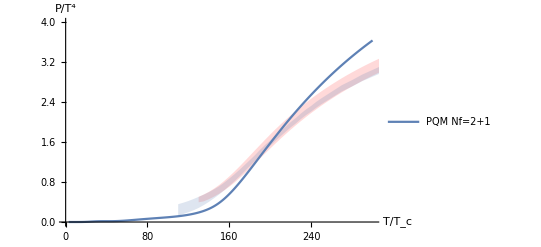

```mathematica
chi0=-Flatten[Import["./TemB1/BUFFER/VTOTAL.DAT"]];
T=Flatten[Table[i,{i,1,Length[chi0]}]];
PlotP=Show[ListLinePlot[{Transpose[{T/1,(chi0-chi0[[1]])/T^4}],Hotpdown,Hotpup},Filling->{2->{3}},FillingStyle->LightRed,PlotStyle->{Automatic,None,None},PlotLegends->{"PQM Nf=2+1"},PlotRange->{{0.,300},{0,4}}],ListLinePlot[{WBdown,WBup},Filling->{1->{2}},PlotStyle->{None}],AxesLabel->{"T/T_c","P/T^4"}]
```